```mathematica
(* We want to generate the 1-loop corrections for Compton scattering *)
```

```mathematica
(* Step 1: Load the FeynArts package *)
```

```mathematica
<<FeynArts`
```

FeynArts 3.10 (21 Jan 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
(* Step 2: Generate topologies with 1 loops, 2 incoming particles, and 2 outgoing particles *)
```

```mathematica
mytops=CreateTopologies[1,2->2]
```

TopologyList[1]
 |  |  |  |

> Top. 1 aebf/cgdg/efegfg.m, 1 diagram

> Top. 2 aebf/cgdf/egefgf.m, 1 diagram

> Top. 3 aebf/cfdg/egefgf.m, 1 diagram

> Top. 4 aebf/cgde/fgfege.m, 1 diagram

> Top. 5 aebf/cedg/fgfege.m, 1 diagram

> Top. 6 aebe/cfdg/fgfege.m, 1 diagram

> Top. 7 aebe/cfdg/ehfgfhgh.m, 1 diagram

> Top. 8 aebf/cedg/ehfgfhgh.m, 1 diagram

> Top. 9 aebf/cfdg/fhegehgh.m, 1 diagram

> Top. 10 aebf/cgde/ehfgfhgh.m, 1 diagram

> Top. 11 aebf/cgdf/fhegehgh.m, 1 diagram

> Top. 12 aebf/cgdg/ghefehfh.m, 1 diagram

> Top. 13 aebf/cgdh/efegfhgh.m, 1 diagram

> Top. 14 aebf/cgdh/efehfggh.m, 1 diagram

> Top. 15 aebf/cgdh/egehfgfh.m, 1 diagram

> Top. 16 aebe/cedf/efff.m, 1 diagram

> Top. 17 aebe/cfde/efff.m, 1 diagram

> Top. 18 aebe/cfdf/efef.m, 1 diagram

> Top. 19 aebf/cede/efff.m, 1 diagram

> Top. 20 aebf/cedf/efef.m, 1 diagram

> Top. 21 aebf/cfde/efef.m, 1 diagram

> Top. 22 aebf/cfdf/efee.m, 1 diagram

> Top. 23 aebe/cfdf/egfggg.m, 1 diagram

> Top. 24 aebe/cfdg/effggg.m, 1 diagram

> Top. 25 aebe/cfdg/egfgfg.m, 1 diagram

> Top. 26 aebe/cfdg/eggfff.m, 1 diagram

> Top. 27 aebe/cfdg/efgfgf.m, 1 diagram

> Top. 28 aebe/cfdf/eggfgf.m, 1 diagram

> Top. 29 aebe/cfdf/efgfgg.m, 1 diagram

> Top. 30 aebf/cedf/egfggg.m, 1 diagram

> Top. 31 aebf/cedg/effggg.m, 1 diagram

> Top. 32 aebf/cedg/egfgfg.m, 1 diagram

> Top. 33 aebf/cfde/egfggg.m, 1 diagram

> Top. 34 aebf/cfdg/efeggg.m, 1 diagram

> Top. 35 aebf/cfdg/fgegeg.m, 1 diagram

> Top. 36 aebf/cgde/effggg.m, 1 diagram

> Top. 37 aebf/cgde/egfgfg.m, 1 diagram

> Top. 38 aebf/cgdf/efeggg.m, 1 diagram

> Top. 39 aebf/cgdf/fgegeg.m, 1 diagram

> Top. 40 aebf/cedg/eggfff.m, 1 diagram

> Top. 41 aebf/cedg/efgfgf.m, 1 diagram

> Top. 42 aebf/cedf/eggfgf.m, 1 diagram

> Top. 43 aebf/cedf/efgfgg.m, 1 diagram

> Top. 44 aebf/cgde/eggfff.m, 1 diagram

> Top. 45 aebf/cgde/efgfgf.m, 1 diagram

> Top. 46 aebf/cgdg/egefff.m, 1 diagram

> Top. 47 aebf/cgdg/gfefef.m, 1 diagram

> Top. 48 aebf/cfde/eggfgf.m, 1 diagram

> Top. 49 aebf/cfde/efgfgg.m, 1 diagram

> Top. 50 aebf/cfdf/egefgg.m, 1 diagram

> Top. 51 aebf/cfdf/gfegeg.m, 1 diagram

> Top. 52 aebf/cfdg/fggeee.m, 1 diagram

> Top. 53 aebf/cfdg/fegege.m, 1 diagram

> Top. 54 aebf/cfde/fggege.m, 1 diagram

> Top. 55 aebf/cfde/fegegg.m, 1 diagram

> Top. 56 aebf/cgdf/fggeee.m, 1 diagram

> Top. 57 aebf/cgdf/fegege.m, 1 diagram

> Top. 58 aebf/cgdg/fgfeee.m, 1 diagram

> Top. 59 aebf/cgdg/gefefe.m, 1 diagram

> Top. 60 aebf/cedf/fggege.m, 1 diagram

> Top. 61 aebf/cedf/fegegg.m, 1 diagram

> Top. 62 aebf/cede/fgfegg.m, 1 diagram

> Top. 63 aebf/cede/gefgfg.m, 1 diagram

> Top. 64 aebe/cfdf/fggege.m, 1 diagram

> Top. 65 aebe/cfdf/fegegg.m, 1 diagram

> Top. 66 aebe/cfde/fgfegg.m, 1 diagram

> Top. 67 aebe/cfde/gefgfg.m, 1 diagram

> Top. 68 aebe/cedf/fgfegg.m, 1 diagram

> Top. 69 aebe/cedf/gefgfg.m, 1 diagram

> Top. 70 aebe/cfdf/egfgghhh.m, 1 diagram

> Top. 71 aebe/cfdf/egfhghgh.m, 1 diagram

> Top. 72 aebe/cfdg/effgghhh.m, 1 diagram

> Top. 73 aebe/cfdg/effhghgh.m, 1 diagram

> Top. 74 aebe/cfdg/egfgfhhh.m, 1 diagram

> Top. 75 aebe/cfdg/egghfhfh.m, 1 diagram

> Top. 76 aebf/cedf/egfgghhh.m, 1 diagram

> Top. 77 aebf/cedf/egfhghgh.m, 1 diagram

> Top. 78 aebf/cedg/effgghhh.m, 1 diagram

> Top. 79 aebf/cedg/effhghgh.m, 1 diagram

> Top. 80 aebf/cedg/egfgfhhh.m, 1 diagram

> Top. 81 aebf/cedg/egghfhfh.m, 1 diagram

> Top. 82 aebf/cfde/egfgghhh.m, 1 diagram

> Top. 83 aebf/cfde/egfhghgh.m, 1 diagram

> Top. 84 aebf/cfdg/efegghhh.m, 1 diagram

> Top. 85 aebf/cfdg/efehghgh.m, 1 diagram

> Top. 86 aebf/cfdg/egehfghh.m, 1 diagram

> Top. 87 aebf/cfdg/fggheheh.m, 1 diagram

> Top. 88 aebf/cgde/effgghhh.m, 1 diagram

> Top. 89 aebf/cgde/effhghgh.m, 1 diagram

> Top. 90 aebf/cgde/egfgfhhh.m, 1 diagram

> Top. 91 aebf/cgde/egghfhfh.m, 1 diagram

> Top. 92 aebf/cgdf/efegghhh.m, 1 diagram

> Top. 93 aebf/cgdf/efehghgh.m, 1 diagram

> Top. 94 aebf/cgdf/egehfghh.m, 1 diagram

> Top. 95 aebf/cgdf/fggheheh.m, 1 diagram

> Top. 96 aebf/cgdg/efegfhhh.m, 1 diagram

> Top. 97 aebf/cgdg/efehfghh.m, 1 diagram

> Top. 98 aebf/cgdg/egehfhfh.m, 1 diagram

> Top. 99 aebf/cgdg/fgfheheh.m, 1 diagram

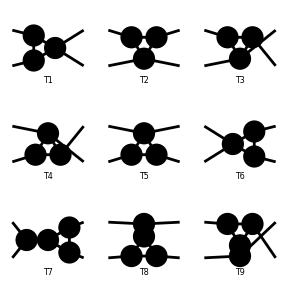

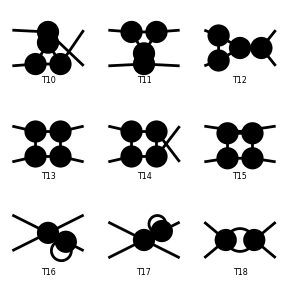

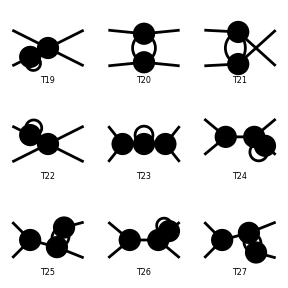

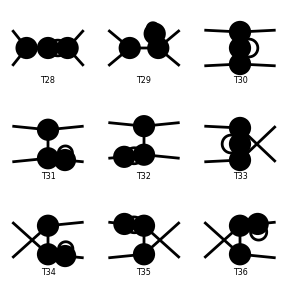

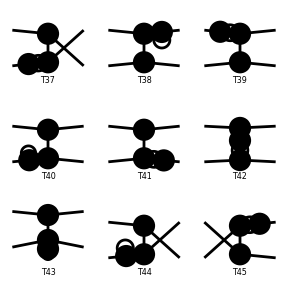

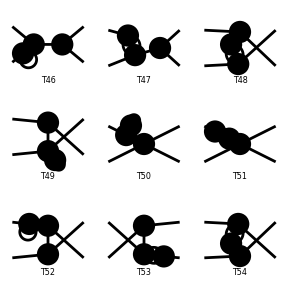

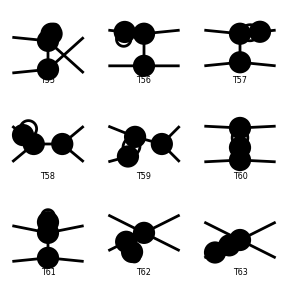

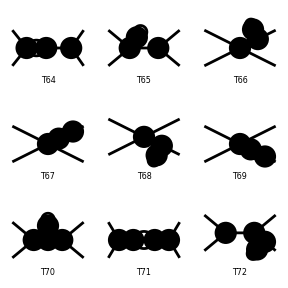

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | [T14] | [T15]
[T16] | [T17] | [T18]),([T19] | [T20] | [T21]
[T22] | [T23] | [T24]
[T25] | [T26] | [T27]),([T28] | [T29] | [T30]
[T31] | [T32] | [T33]
[T34] | [T35] | [T36]),([T37] | [T38] | [T39]
[T40] | [T41] | [T42]
[T43] | [T44] | [T45]),([T46] | [T47] | [T48]
[T49] | [T50] | [T51]
[T52] | [T53] | [T54]),([T55] | [T56] | [T57]
[T58] | [T59] | [T60]
[T61] | [T62] | [T63]),([T64] | [T65] | [T66]
[T67] | [T68] | [T69]
[T70] | [T71] | [T72]),([T73] | [T74] | [T75]
[T76] | [T77] | [T78]
[T79] | [T80] | [T81]),([T82] | [T83] | [T84]
[T85] | [T86] | [T87]
[T88] | [T89] | [T90]),([T91] | [T92] | [T93]
[T94] | [T95] | [T96]
[T97] | [T98] | [T99])]

```mathematica
Paint[mytops]
```

```mathematica
(* Step 3: Insert the fields. We have a photon (vector boson, V[1]) and electron (first generation fermion, F[1]) going to a photon and an electron and this is a QED process *)
```

```mathematica
mydiags=InsertFields[mytops,{V[1],F[1]}->{V[1],F[1]},Model->"QED",InsertionLevel->{Classes}]
```

loading generic model file /home/leon/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/leon/FeynArts-3.10/Models/QED.mod

> 7 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counterterms of order 1

classes model {QED} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 1 Classes insertion

> Top. 8: 0 Classes insertions

> Top. 9: 1 Classes insertion

> Top. 10: 1 Classes insertion

> Top. 11: 2 Classes insertions

> Top. 12: 1 Classes insertion

> Top. 13: 1 Classes insertion

> Top. 14: 0 Classes insertions

> Top. 15: 1 Classes insertion

> Top. 16: 0 Classes insertions

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

> Top. 26: 0 Classes insertions

> Top. 27: 0 Classes insertions

> Top. 28: 0 Classes insertions

> Top. 29: 0 Classes insertions

> Top. 30: 0 Classes insertions

> Top. 31: 0 Classes insertions

> Top. 32: 0 Classes insertions

> Top. 33: 0 Classes insertions

> Top. 34: 0 Classes insertions

> Top. 35: 0 Classes insertions

> Top. 36: 0 Classes insertions

> Top. 37: 0 Classes insertions

> Top. 38: 0 Classes insertions

> Top. 39: 0 Classes insertions

> Top. 40: 0 Classes insertions

> Top. 41: 0 Classes insertions

> Top. 42: 0 Classes insertions

> Top. 43: 0 Classes insertions

> Top. 44: 0 Classes insertions

> Top. 45: 0 Classes insertions

> Top. 46: 0 Classes insertions

> Top. 47: 0 Classes insertions

> Top. 48: 0 Classes insertions

> Top. 49: 0 Classes insertions

> Top. 50: 0 Classes insertions

> Top. 51: 0 Classes insertions

> Top. 52: 0 Classes insertions

> Top. 53: 0 Classes insertions

> Top. 54: 0 Classes insertions

> Top. 55: 0 Classes insertions

> Top. 56: 0 Classes insertions

> Top. 57: 0 Classes insertions

> Top. 58: 0 Classes insertions

> Top. 59: 0 Classes insertions

> Top. 60: 0 Classes insertions

> Top. 61: 0 Classes insertions

> Top. 62: 0 Classes insertions

> Top. 63: 0 Classes insertions

> Top. 64: 0 Classes insertions

> Top. 65: 0 Classes insertions

> Top. 66: 0 Classes insertions

> Top. 67: 0 Classes insertions

> Top. 68: 0 Classes insertions

> Top. 69: 0 Classes insertions

> Top. 70: 1 Classes insertion

> Top. 71: 1 Classes insertion

> Top. 72: 1 Classes insertion

> Top. 73: 1 Classes insertion

> Top. 74: 0 Classes insertions

> Top. 75: 1 Classes insertion

> Top. 76: 0 Classes insertions

> Top. 77: 0 Classes insertions

> Top. 78: 0 Classes insertions

> Top. 79: 0 Classes insertions

> Top. 80: 0 Classes insertions

> Top. 81: 0 Classes insertions

> Top. 82: 1 Classes insertion

> Top. 83: 1 Classes insertion

> Top. 84: 1 Classes insertion

> Top. 85: 1 Classes insertion

> Top. 86: 0 Classes insertions

> Top. 87: 1 Classes insertion

> Top. 88: 0 Classes insertions

> Top. 89: 1 Classes insertion

> Top. 90: 1 Classes insertion

> Top. 91: 1 Classes insertion

> Top. 92: 0 Classes insertions

> Top. 93: 0 Classes insertions

> Top. 94: 0 Classes insertions

> Top. 95: 0 Classes insertions

> Top. 96: 1 Classes insertion

> Top. 97: 0 Classes insertions

> Top. 98: 1 Classes insertion

> Top. 99: 1 Classes insertion

in total: 24 Classes insertions

TopologyList[Process→{V[1],F[1,{Gen2}]}→{V[1],F[1,{Gen4}]},Model→{QED},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→F[1,{Gen4}],Field[7]→-F[1,{Gen2}],Field[8]→V[1]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→F[1,{Gen4}],Field[7]→-F[1,{Gen2}],Field[8]→V[1]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→F[1,{Gen2}],Field[7]→V[1],Field[8]→F[1,{Gen4}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→V,Field[6]→F,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→V[1],Field[6]→-F[1,{Gen5}],Field[7]→F[1,{Gen5}],Field[8]→-F[1,{Gen5}]],FeynmanGraph[1,Classes==2][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→V[1],Field[6]→F[1,{Gen5}],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→-F[1,{Gen2}],Field[7]→F[1,{Gen4}],Field[8]→V[1]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][8],Field[4]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}],Field[6]→F[1,{Gen2}],Field[7]→V[1],Field[8]→F[1,{Gen4}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][8],Field[4]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][7],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→F[1,{Gen4}],Field[7]→F[1,{Gen2}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][8],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→-F[1,{Gen4}],Field[7]→V[1],Field[8]→-F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→-F[1,{Gen4}],Field[7]→F[1,{Gen2}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][8],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→F[1,{Gen4}],Field[7]→V[1],Field[8]→-F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→F[1,{Gen2}],Field[7]→-F[1,{Gen4}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→V,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→V[1],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][8],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→F[1,{Gen2}],Field[7]→V[1],Field[8]→-F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→F[1,{Gen2}],Field[7]→-F[1,{Gen4}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][8],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}],Field[6]→F[1,{Gen4}],Field[7]→V[1],Field[8]→-F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][5],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}],Field[6]→F[1,{Gen2}],Field[7]→-F[1,{Gen4}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→V,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→V[1],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→V,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}],Field[6]→V[1],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][8],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→F[1,{Gen2}],Field[7]→V[1],Field[8]→-F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→-F[1,{Gen4}],Field[7]→F[1,{Gen2}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][8],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}],Field[6]→F[1,{Gen4}],Field[7]→V[1],Field[8]→-F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][5],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen4}],Field[6]→-F[1,{Gen4}],Field[7]→F[1,{Gen2}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→V,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→V[1],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]]]

> Top. 1 aebe/cfdg/ehfgfhgh.m, 1 diagram

> Top. 2 aebf/cfdg/fhegehgh.m, 1 diagram

> Top. 3 aebf/cgde/ehfgfhgh.m, 1 diagram

> Top. 4 aebf/cgdf/fhegehgh.m, 2 diagrams

> Top. 5 aebf/cgdg/ghefehfh.m, 1 diagram

> Top. 6 aebf/cgdh/efegfhgh.m, 1 diagram

> Top. 7 aebf/cgdh/egehfgfh.m, 1 diagram

> Top. 8 aebe/cfdf/egfgghhh.m, 1 diagram

> Top. 9 aebe/cfdf/egfhghgh.m, 1 diagram

> Top. 10 aebe/cfdg/effgghhh.m, 1 diagram

> Top. 11 aebe/cfdg/effhghgh.m, 1 diagram

> Top. 12 aebe/cfdg/egghfhfh.m, 1 diagram

> Top. 13 aebf/cfde/egfgghhh.m, 1 diagram

> Top. 14 aebf/cfde/egfhghgh.m, 1 diagram

> Top. 15 aebf/cfdg/efegghhh.m, 1 diagram

> Top. 16 aebf/cfdg/efehghgh.m, 1 diagram

> Top. 17 aebf/cfdg/fggheheh.m, 1 diagram

> Top. 18 aebf/cgde/effhghgh.m, 1 diagram

> Top. 19 aebf/cgde/egfgfhhh.m, 1 diagram

> Top. 20 aebf/cgde/egghfhfh.m, 1 diagram

> Top. 21 aebf/cgdg/efegfhhh.m, 1 diagram

> Top. 22 aebf/cgdg/egehfhfh.m, 1 diagram

> Top. 23 aebf/cgdg/fgfheheh.m, 1 diagram

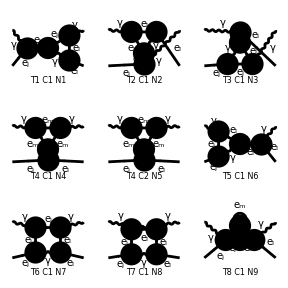

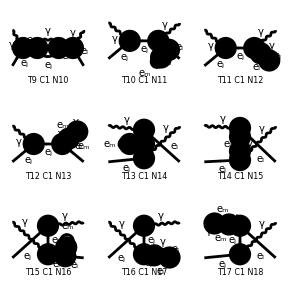

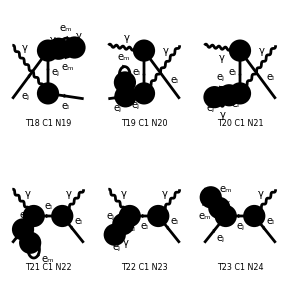

FeynArtsGraphics[{\gamma,ComposedChar[e,j]}→{\gamma,ComposedChar[e,l]}][([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3]
[T4 C1 N4] | [T4 C2 N5] | [T5 C1 N6]
[T6 C1 N7] | [T7 C1 N8] | [T8 C1 N9]),([T9 C1 N10] | [T10 C1 N11] | [T11 C1 N12]
[T12 C1 N13] | [T13 C1 N14] | [T14 C1 N15]
[T15 C1 N16] | [T16 C1 N17] | [T17 C1 N18]),([T18 C1 N19] | [T19 C1 N20] | [T20 C1 N21]
[T21 C1 N22] | [T22 C1 N23] | [T23 C1 N24]
Null | Null | Null)]

```mathematica
Paint[mydiags]
```

```mathematica
(* Step 4: Select the diagrams corresponding to Compton scattering *)
```

```mathematica
Compton=DiagramExtract[mydiags,{1,5,6,7,10,12,13,23,24}]
```

TopologyList[Process→{V[1],F[1,{Gen2}]}→{V[1],F[1,{Gen4}]},Model→{QED},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→F[1,{Gen4}],Field[7]→-F[1,{Gen2}],Field[8]→V[1]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→V,Field[6]→F,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==2][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→V[1],Field[6]→F[1,{Gen5}],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen4}],Field[6]→-F[1,{Gen2}],Field[7]→F[1,{Gen4}],Field[8]→V[1]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][8],Field[4]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→V,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→-F[1,{Gen2}],Field[6]→F[1,{Gen2}],Field[7]→V[1],Field[8]→F[1,{Gen4}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→-F[1,{Gen4}],Field[7]→F[1,{Gen2}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][7],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→F[1,{Gen2}],Field[7]→-F[1,{Gen4}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][7],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→V,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→V[1],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][5],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][6],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→F,Field[7]→F,Field[8]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen4}],Field[6]→-F[1,{Gen4}],Field[7]→F[1,{Gen2}],Field[8]→V[1]]]],Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][7],Field[4]],Propagator[Internal][Vertex[3][6],Vertex[3][7],Field[5]],Propagator[Internal][Vertex[3][6],Vertex[3][8],Field[6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[7]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][8],Field[8]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F,Field[6]→V,Field[7]→F,Field[8]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→F[1,{Gen2}],Field[3]→V[1],Field[4]→-F[1,{Gen4}],Field[5]→F[1,{Gen2}],Field[6]→V[1],Field[7]→-F[1,{Gen5}],Field[8]→F[1,{Gen5}]]]]]

> Top. 1 aebe/cfdg/ehfgfhgh.m, 1 diagram

> Top. 2 aebf/cgdf/fhegehgh.m, 1 diagram

> Top. 3 aebf/cgdg/ghefehfh.m, 1 diagram

> Top. 4 aebf/cgdh/efegfhgh.m, 1 diagram

> Top. 5 aebe/cfdf/egfhghgh.m, 1 diagram

> Top. 6 aebe/cfdg/effhghgh.m, 1 diagram

> Top. 7 aebe/cfdg/egghfhfh.m, 1 diagram

> Top. 8 aebf/cgdg/egehfhfh.m, 1 diagram

> Top. 9 aebf/cgdg/fgfheheh.m, 1 diagram

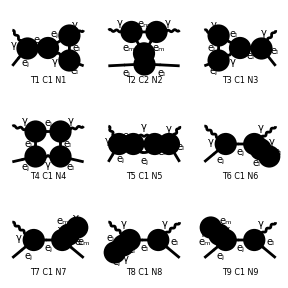

FeynArtsGraphics[{\gamma,ComposedChar[e,j]}→{\gamma,ComposedChar[e,l]}][([T1 C1 N1] | [T2 C2 N2] | [T3 C1 N3]
[T4 C1 N4] | [T5 C1 N5] | [T6 C1 N6]
[T7 C1 N7] | [T8 C1 N8] | [T9 C1 N9])]

```mathematica
Diagrams=Paint[Compton]
```

```mathematica
(* Export to LaTeX *)
```

```mathematica
Export["compton1L.tex",Diagrams,"TeX"]
```

{compton1L.tex}